## A Guitar String — Blasting into the Stratosphere

## Completed and Analyzed in class, April 8, 2025

This is the seventeenth notebook for you to finish in class.

We are leaving behind the crutch of thinking of continuous systems as chunks. We are going to describe continuous systems as continuous systems, which means imagining the limit that the sizes of the chunks goes to zero while the number of chunks goes to infinity. This is exactly the limit that turns our differences of differences into second derivatives.

But first, we need to get familiar with how Mathematica expects continuous systems to be described. Just as we divided space into chunks, even before that in the course, we began by dividing time into steps and then used Euler’s Method or Second-Order Runge-Kutta to march forward through the discrete steps of time.

In reality, probably all the way down to the unfathomably short amount of time (10^-43 seconds)  known as the Planck time, time is also continuous. Let’s see how we describe time-dependent equations to Mathematica without resorting to time steps. Mathematica will then solve them for us.

So before we get to the guitar string, we are going all the way back to our fourth notebook, the damped harmonic oscillator, and do it a new way.

### But First, Back to the Earth — The Harmonic Oscillator

Back in the fourth notebook, we considered this force law:

F=-20x-v

We combined this with Newton’s Law F=ma with m=5 and then we had

5a=-20x-v

Then we got a bit fancier and more general. First we divided through by the 5. We  could also put all the terms on the left:

a+20/5 x+1/5 v=0

The ratio 20/5 is the ratio of the spring constant to the mass and we called that ω_0^2. So for these constants, ω_0=√(20/5)=2. The ratio1/5 is the ratio of the damping coefficient to the mass and we called that combination 2γ. So for these constants 2γ=1/5 or γ=1/10.  Our equation is now:

a+2γv+ω_0^2 x=0

When ω_0>γ as it is here (2 is definitely greater than 1/10), the system is “underdamped.” The greater the ratio of ω_0/γ the more oscillations occur for each  1/e-folding of the envelope of the oscillation as its motion damps toward nothing. We went through all this many weeks back, and I am giving you a quick refresher, but now we want to rediscover these facts, but by forcing Mathematica to do the hard work.

We have one more step, which is to introduce the notation of derivatives.

The velocity v is the rate of change (with respect to time) of the position x. Meanwhile the acceleration a is the rate of change (with respect to time) of the velocity v. The rate of change is called the derivative. To say that you want to take a derivative of x(t) with respect to t in Mathematica, you write:

```mathematica
Derivative[1][x][t];
```

This says take one derivative of the function x with respect to its argument, and evaluate the resulting function at time t. So far we haven’t done anything at all with our symbolic expression. One thing we can do with it is just display it in a pretty form:

```mathematica
Derivative[1][x][t] // TraditionalForm
```

x'(t)

The afterthought of TraditionalForm says that you would like to see the result as it would be likely to be typeset in a mathematics or physics textbook. Note that physicists (and older mathematicians) often use a different notation for the first derivative, which is known as Leibniz notation. We have our hands full. Let’s not add yet more notations into the mix.

The acceleration is the rate of change of the velocity, and that is the second derivative, and here is how you tell Mathematica you want to take a second derivative of x with respect to t:

```mathematica
Derivative[2][x][t] // TraditionalForm
```

x''(t)

Here is how you write the whole harmonic oscillator equation, which was a+2γv+ω_0^2 x=0, in a way that Mathematica can unambiguously understand it:

```mathematica
Derivative[2][x][t]+2gamma Derivative[1][x][t]+omega0^2 x[t]==0 // TraditionalForm
```

2 gamma x'(t)+omega0^2 x(t)+x''(t)==0

Notice extremely carefully the use of == rather than = in the equation for the derivative. We are not making an assignment! We are making a conditional test, and Mathematica is going to do its best to approximately satisfy that conditional test when (deep under the hood) it applies some differential equation solving strategy like Euler, or Runge-Kutta Second Order, or maybe Runge-Kutta Fourth Order (that I never got around to introducing, because it is a mess, even for me, and because Runge-Kutta Second Order was serving us very well).

Now let’s also define omega0 and gamma for Mathematica, and also add some initial conditions on the position and velocity:

```mathematica
Module[{omega0=2, gamma=1/10},{Derivative[2][x][t]+2gamma Derivative[1][x][t]+omega0^2 x[t]==0,x[0]==0,Derivative[1][x][0]==3}] // TraditionalForm
```

{x''(t)+(x'(t))/5+4 x(t)==0,x(0)==0,x'(0)==3}

I set the initial position at t=0 as 0 and I set the initial velocity as 3. Again, it is extremely important to use == rather than =. If you screw that up, it is quit and restart time.

We have failed to do one minor thing. We have set up a pile of equations, but we haven’t given this pile of equations any name, so we can’t use them anywhere else. Let’s give them a name:

```mathematica
harmonicOscillatorProblem=Module[{omega0=2, gamma=1/10},{Derivative[2][x][t]+2gamma Derivative[1][x][t]+omega0^2 x[t]==0,x[0]==0,Derivative[1][x][0]==3}] ;
```

```mathematica
harmonicOscillatorProblem//TraditionalForm
```

{x''(t)+(x'(t))/5+4 x(t)==0,x(0)==0,x'(0)==3}

### Making Mathematica Do The Hard Work

This particular problem is exactly solvable. So you can tell Mathematica to try to exactly solve it using DSolve, and lo and behold, it succeeds:

```mathematica
DSolve[harmonicOscillatorProblem]
```

{{x[t]→10 √(3/133) ⅇ^(-t/10) Sin[(√399 t)/10]}}

Notice that what is output is a list of lists of rules. All that generality is in case you have multiple functions being solved simultaneously. We just have one function, so we grab the first and only list of rules out of the list of lists of rules:

```mathematica
harmonicOscillatorSolutionRule = DSolve[harmonicOscillatorProblem][[1]];
```

```mathematica
harmonicOscillatorSolutionRule
```

{x[t]→10 √(3/133) ⅇ^(-t/10) Sin[(√399 t)/10]}

We still don’t have something we can plot. YOu don’t plot a rule. We have to turn the rule into a function, and I’ll call that function harmonicOscillatorSolution:

```mathematica
harmonicOscillatorSolution[t_]=x[t]/.harmonicOscillatorSolutionRule
```

10 √(3/133) ⅇ^(-t/10) Sin[(√399 t)/10]

Finally, we plot the solution:

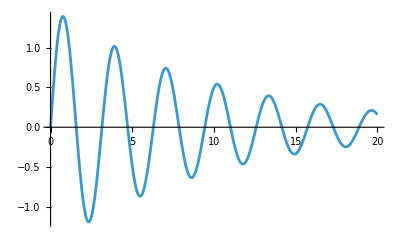

```mathematica
Plot[harmonicOscillatorSolution[t],{t,0,20}]
```

```mathematica
oscillatorGraphic[displacement_]:=Graphics[{
EdgeForm[Thin],White,
RegularPolygon[{0.0,0.0},2,4],
Black,
Point[{0,0}],
Point[{displacement,0}]
}]
oscillatorGraphic[1.0]
```

-Graphics-

```mathematica
Animate[oscillatorGraphic[harmonicOscillatorSolution[t]],{t, 0, 20},DefaultDuration->20]
```